# Problem Set 1

## for February 09, 23.59, 2024

## Problem 1, Time delayed model with Allee effect It is well-known that individuals in many biological populations suffer from a reduced capacity to reproduce or survive when the population density (that is, size) is small. As a consequence, the population may experience extinction depending on its density. This effect is known as Allee effect [W. C. Allee et al. Principles of animal ecology (1949)]. The Allee effect can arise due to several different mechanisms, such as difficulty of finding a mate, inefficient antipredator strategies in small groups of prey (due to reduced cooperation) etc. Mechanisms that allow for the Allee effect to appear (for example reduced cooperation) are often time delayed. Denoting the population size by N, a time-delayed growth with Allee effect can be modelled as follows: Here is a time-delay parameter. Your task is to analyse how the dynamics in this model depends on the time-delay parameter . Solve Eq. (1) numerically. Integrate Eq. (1) for , up to 5. Set the remaining parameters to: , , , and (where denotes the population size at time t = 0). Assume further that during the time interval the population size was constant and equal to .

## a) Show examples of the different dynamics obtained in this model: no oscillations, damped oscillations, and stable oscillations (limit cycle).

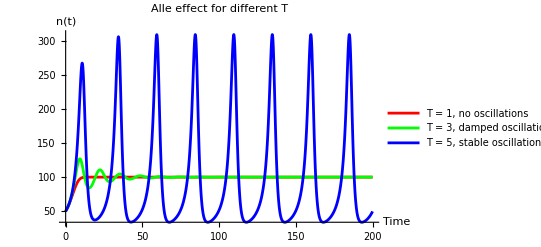

```mathematica
ClearAll["Global`*"];
A = 20;
K = 100;
r = 0.1;
initialCondition = n[0] == 50;
TValues = {1, 3, 5};
t0 = 0;
tMax = 200;

solveDifferentialEquation[T_] := NDSolveValue[
	{n'[t] == r*n[t]*(1 - n[t - T]/K)*(n[t]/A - 1), initialCondition}, 
    n, {t, t0, tMax}
];

solutions = Table[
	solveDifferentialEquation[T], 
	{T, TValues}
];

legends = {
	"T = 1, no oscillations", 
	"T = 3, damped oscillations", 
	"T = 5, stable oscillations (limit cycles)"
};

colors = {
	Red,
	Green,
	Blue
};

Plot[Evaluate[Table[solutions[[i]][t], {i, Length[TValues]}]], {t, t0, tMax},
     PlotRange -> All, 
     PlotLegends -> legends, 
     PlotLabel -> "Alle effect for different T", 
     AxesLabel -> {"Time", "n(t)"},
     PlotStyle->colors
]
```

## b) Estimate numerically with one decimal precision the value of T at which the dynamics starts exhibiting damped oscillations.

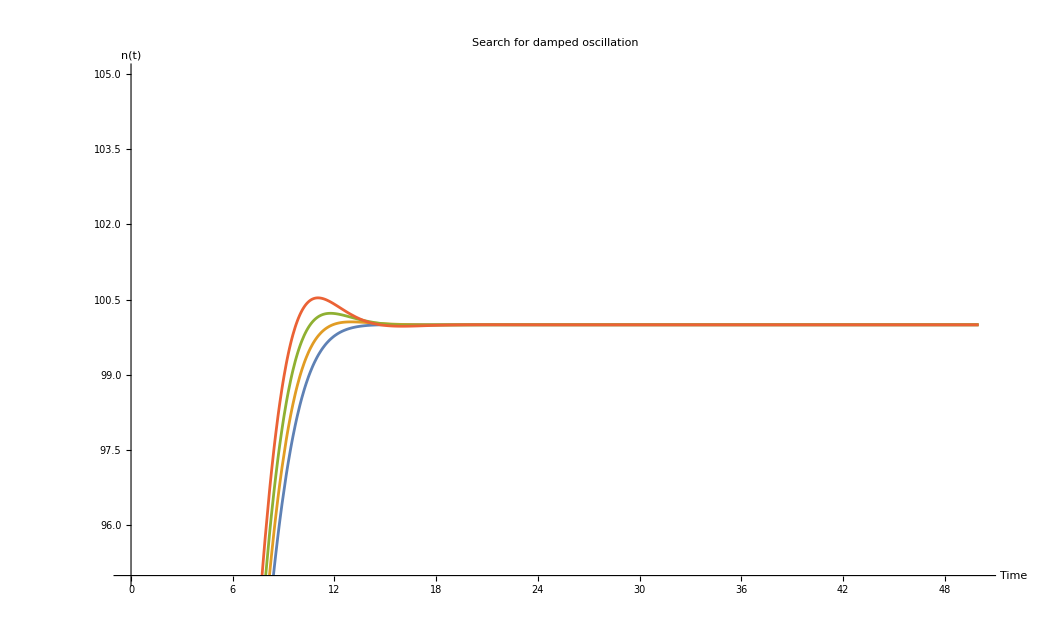

```mathematica
ClearAll["Global`*"];
A = 20;
K = 100;
r = 0.1;
initialCondition = n[0] == 50;
TValues = {1, 1.1, 1.2, 1.3};
t0 = 0;
tMax = 50;

solveDifferentialEquation[T_] := NDSolveValue[
    {n'[t] == r*n[t]*(1 - n[t - T]/K)*(n[t]/A - 1), initialCondition}, 
    n, {t, t0, tMax}
];

solutions = Table[
    solveDifferentialEquation[T], 
    {T, TValues}
];

Plot[Evaluate[Table[solutions[[i]][t], {i, Length[TValues]}]], {t, t0, tMax},
     PlotRange -> {{t0, tMax}, {95, 105}}, 
     PlotLabel -> "Search for damped oscillation", 
     AxesLabel -> {"Time", "n(t)"}
]
```

From the plot it seem evident that the damped oscillation starts as soon as .

## c) Estimate numerically with one decimal precision the value of T (denoted by TH) at which a bifurcation (Hopf bifurcation) occurs.

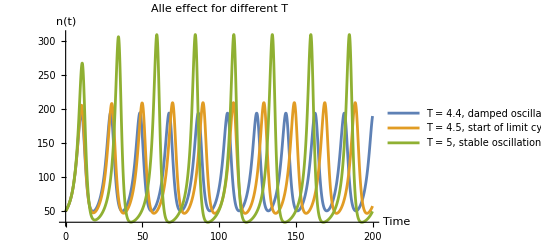

```mathematica
ClearAll["Global`*"];
A = 20;
K = 100;
r = 0.1;
initialCondition = n[0] == 50;
TValues = {4.4,4.5, 5};
t0 = 0;
tMax = 200;

solveDifferentialEquation[T_] := NDSolveValue[
	{n'[t] == r*n[t]*(1 - n[t - T]/K)*(n[t]/A - 1), initialCondition}, 
    n, {t, t0, tMax}
];

solutions = Table[
	solveDifferentialEquation[T], 
	{T, TValues}
];

legends = {
	"T = 4.4, damped oscillations", 
	"T = 4.5, start of limit cycle", 
	"T = 5, stable oscillations (limit cycles)"
};


Plot[Evaluate[Table[solutions[[i]][t], {i, Length[TValues]}]], {t, t0, tMax},
     PlotRange -> All, 
     PlotLegends->legends,
     PlotLabel -> "Alle effect for different T", 
     AxesLabel -> {"Time", "n(t)"}
]
```

In the plot there are shown the cases  of damped oscillation (that show stable oscillations),  the conversion from damped oscillations  to limit cycles, and  true stable oscillations, limit cycles.

## d) Use linear stability analysis to analytically compute the value of . Do this by linearising Eq. (1) around the steady state and use a perturbation that is proportional to . Compare that you obtain analytically to the estimate found in subtask c). Discuss your results.

```mathematica
ClearAll["Global`*"];
alleEq = n'[t] == r*n[t]*(1 - n[t - T]/K)*(n[t]/A - 1);
rhs = alleEq[[2]]

D[rhs, n[t]]
```

r n[t] (-1+n[t]/A) (1-1/100 n[t-T])

(r n[t] (1-1/100 n[t-T]))/A+r (-1+n[t]/A) (1-1/100 n[t-T])

## Problem 2, Discrete growth models [5p] Assume that the population size depends on discrete time (τ = 0,1,2,...) as follows Here, the parameters satisfy: , , and .

## a) Analytically determine the non-negative steady states (fixed points) of the model (2).

There is a trivial fixed point at , and there is a fixed point at  which can be found by setting  and solving for .

## b) Perform linear stability analysis and discuss how the linear stability of the non-negative steady states depends on the parameters.

To solve this one needs to take the derivative of the growth model which corresponds to:
 
 Now insert the  and the resulting derivative is:

For non-negative fixed points it follows that if  then the fixed point is stable and if  then the fixed point is unstable. If one inserts b = 1 to the solution one can see that the fixed point will always be stable for the parameters given.

## c) Analytically find all conditions on the parameters (within their ranges of validity) where a bifurcation from a stable steady state to an unstable steady state occurs.

## In the following, use the parameter values: and . d) Investigate how the population size depends on time for the following values of the initial population size: and 10. For each case, use the linear stability analysis performed in task b) to approximate the population dynamics in the vicinity of the unstable steady state. [Hint: treat the initial condition as a small perturbation around the unstable steady state, and plot how this perturbation, and consequently the population size, is expected to change over time according to the linear stability analysis.] Plot this approximation together with the corresponding (exact) population dynamics obtained by iterating Eq. (2). Use log-log scale for plotting to distinguish well between the different curves.

As already hinted at in sub task b) the fixed point in question must be stable due to the fact that , and thus the derivative of the growth will remain negative for all values of . One can see the behaviour in the following plots.

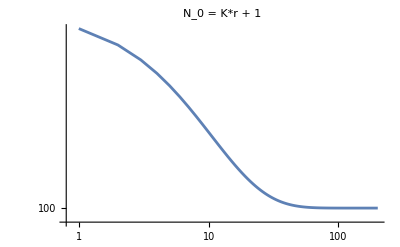

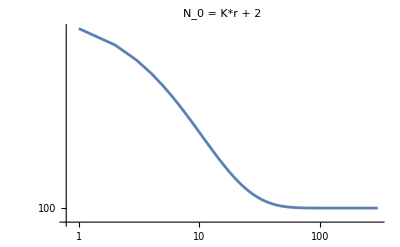

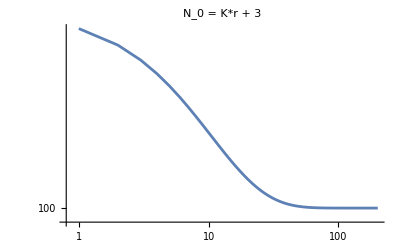

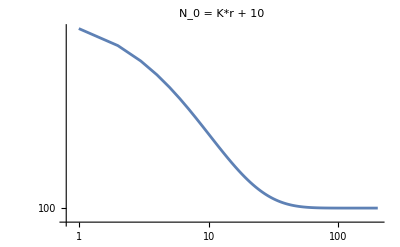

```mathematica
ClearAll["Global`*"];
b = 1;
k = 10^3;
r = 0.1;

data1 = NestList[{((r+1)*#[[1]])/(1+((#[[1]])/k)^b)} &, {k*r+1}, 200];
data2 = NestList[{((r+1)*#[[1]])/(1+((#[[1]])/k)^b)} &, {k*r+2}, 300];
data3 = NestList[{((r+1)*#[[1]])/(1+((#[[1]])/k)^b)} &, {k*r+3}, 200];
data4 = NestList[{((r+1)*#[[1]])/(1+((#[[1]])/k)^b)} &, {k*r+10}, 200];

pairedData1 = MapIndexed[{First[#2], #[[1]]} &, data1];
pairedData2 = MapIndexed[{First[#2], #[[1]]} &, data2];
pairedData3 = MapIndexed[{First[#2], #[[1]]} &, data3];
pairedData4 = MapIndexed[{First[#2], #[[1]]} &, data4];

Plot1 = ListLogLogPlot[{pairedData1}, PlotLabel -> "N_0 = K*r + 1", Joined -> True]
Plot2 = ListLogLogPlot[{pairedData2}, PlotLabel -> "N_0 = K*r + 2", Joined -> True]
Plot3 = ListLogLogPlot[{pairedData3}, PlotLabel -> "N_0 = K*r + 3", Joined -> True]
Plot4 = ListLogLogPlot[{pairedData4}, PlotLabel -> "N_0 = K*r + 10", Joined -> True]
```

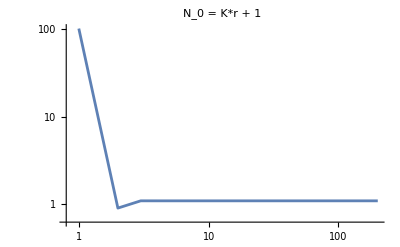

```mathematica
ClearAll["Global`*"];
b = 1;
k = 10^3;
r = 0.1;

data1 = NestList[{(r+1)/(1+((#[[1]])/k)^b)-(b(r+1))/((1+((#[[1]])/k)^b)^2)((#[[1]])/k)^b} &, {k*r+1}, 200];
pairedData1 = MapIndexed[{First[#2], #[[1]]} &, data1];
Plot1 = ListLogLogPlot[{pairedData1}, PlotLabel -> "N_0 = K*r + 1", Joined -> True]
```

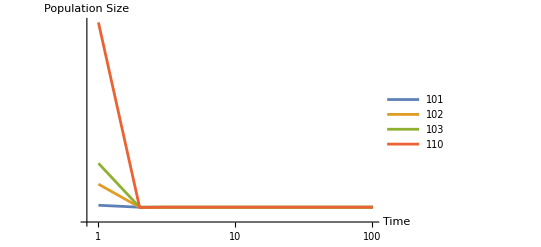

```mathematica
(* Define the linearized function *)
f[n_, r_, k_, b_] := (r + 1)/(1 + (n/k)^b) - (b*(r + 1))/(1 + (n/k)^b)^2 * (n/k)^b;

(* Parameters *)
r = 0.1;
k = 10^3;
b = 1;

(* Steady state *)
steadyState = k*r;

(* Initial conditions *)
initialConditions = {101, 102, 103, 110};  (* Modify as needed *)
timeSteps = 100;  (* Number of time steps to simulate *)

(* Compute dynamics for each initial condition *)
results = Table[
    deltaN = initialConditions[[i]] - steadyState;
    NList = Table[0, {j, 1, timeSteps + 1}];
    NList[[1]] = deltaN + steadyState;
    For[j = 1, j <= timeSteps, j++,
        deltaN = f[NList[[j]], r, k, b];
        NList[[j + 1]] = deltaN + steadyState;
    ];
    NList,
    {i, 1, Length[initialConditions]}
];

(* Plotting the results *)
ListLogLogPlot[results, PlotRange -> All, 
AxesLabel -> {"Time", "Population Size"}, 
PlotLegends -> initialConditions,
Joined->True
]
```

## e) Discuss how well the stability analysis approximates the exact dynamics. How does the initial condition influence the approximation?

Noch keinen blassen Schimmer einer Ahnung was man hier  eigentlich genau machen soll.

## f) Use linear stability analysis to approximate the dynamics in the vicinity of the stable steady state. Use initial population size , where is the value of the stable steady state and is an initial perturbation around . Choose \delta and 10. Proceed as follows. Starting from an initial perturbation , approximate the dynamics until the system comes close to using the linear stability analysis around the stable steady state. Plot this approximation together with the exact dynamics, starting at . Perform the approximation for the different values of the initial perturbation . How does the initial perturbation influence the approximation?